## MIMO RHP zero (Section 3.8.3)

```mathematica
Clear["Global`*"]
```

```mathematica
G0 = 1/(1+2s)^2 ({{1, 1}, {1+2s, 2}});Det[G0] // Simplify
```

(1-2 s)/(1+2 s)^4

```mathematica
G0a = G0 /. s-> 1/2;  MatrixForm[G0a]
```

(1/4 | 1/4
1/2 | 1/2)

```mathematica
{vals,vecs}=Eigensystem[G0a]; { vals//MatrixForm,vecs//MatrixForm}
```

{(3/4
0),(1/2 | 1
-1 | 1)}

```mathematica
{u,Σ,v} = SingularValueDecomposition[G0a];  MatrixForm/@{u,Σ,v}
```

{(1/(√5) | -2/(√5)
2/(√5) | 1/(√5)),((√(5/2))/2 | 0
0 | 0),(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))}

```mathematica
MatrixForm[u.Σ.vᵀ-G0a]  (* check the SVD *)
```

(0 | 0
0 | 0)

```mathematica
G0tf = TransferFunctionModel[G0,s]
```

1/(1+2 s)^21/(1+2 s)^21/(1+2 s)2/(1+2 s)^2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s22111211111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
tmax = 10;
```

```mathematica
y0a = OutputResponse[G0tf,{(1)UnitStep[t],(0)UnitStep[t]},t] // Simplify
```

{Piecewise[{{1-1/2 ⅇ^(-t/2) (2+t), t≥0}, {0, True}}],(1-ⅇ^(-t/2)) UnitStep[t]}

```mathematica
y0b = OutputResponse[G0tf,{(0)UnitStep[t],(-1)UnitStep[t]},t] // Simplify
```

{Piecewise[{{-1+1/2 ⅇ^(-t/2) (2+t), t≥0}, {0, True}}],-ⅇ^(-t/2) (-2+2 ⅇ^(t/2)-t) UnitStep[t]}

```mathematica
y0c = OutputResponse[G0tf,{(1)UnitStep[t],(-1)UnitStep[t]},t] // Simplify
```

{0,Piecewise[{{-1+ⅇ^(-t/2) (1+t), t≥0}, {0, True}}]}

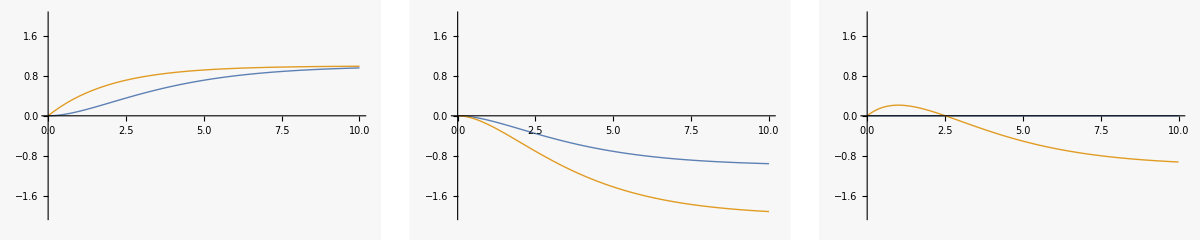

```mathematica
pa=Plot[y0a,{t,0,tmax},PlotRange->{{0,tmax},{-2,2}}];pb=Plot[y0b,{t,0,tmax},PlotRange->{{0,tmax},{-2,2}}];pc=Plot[y0c,{t,0,tmax},PlotRange->{{0,tmax},{-2,2}}];
GraphicsRow[{pa,pb,pc}]
```

```mathematica
y0gen =  OutputResponse[G0tf,{a UnitStep[t],b UnitStep[t]},t] // FullSimplify
```

{1/2 (a+b) (2-ⅇ^(-t/2) (2+t)) UnitStep[t],(a+2 b-ⅇ^(-t/2) (a+b (2+t))) UnitStep[t]}

Show that we can find the zero numerically, too :

```mathematica
sigmas = SingularValueList[G0];
```

```mathematica
FindRoot [sigmas[[1]]==0,{s,0}]
```

{s→0.5}

```mathematica
FindRoot [sigmas[[2]]==0,{s,0}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{s→2.7168×10^29}

above shows that only 1 singular value has a root (zero).  
Below, a graph of σ(s) also shows the root at s=0.5;
note that this kind of graph would not find a complex zero.

```mathematica
G1 = 1/(1+2s)^2({{1, 1, 1}, {1+2s, 2, 1}});
```

```mathematica
sigmas1 = SingularValueList[G1];
```

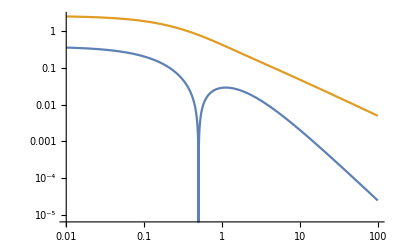
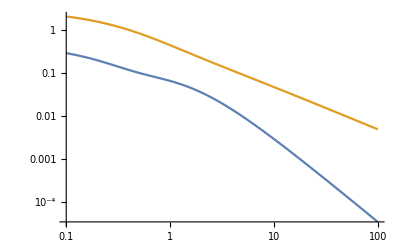

```mathematica
{LogLogPlot[{sigmas[[1]],sigmas[[2]]},{s,0.01,100}],LogLogPlot[{sigmas1[[1]],sigmas1[[2]]},{s,0.1,100}]}
```

## equivalent state space form

```mathematica
sys0 = StateSpaceModel[G0tf]
```

010000-1/4-1001000010000-1/4-1011/401/40001/41/21/2000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2241FalseFalseFalseAutomaticNoneAutomatic

4-dimensional state space  →  if there were 4 inputs or 4 outputs, there could be no zeros.